```mathematica
Clear["Global`*"]
```

## Barbosa [1977] orig func

```mathematica
barbDist[vpar_,vperp_,deltaPhi_,T_,alpha_]:=4/(π^(1/2)Erfc[-√(deltaPhi/T)])Exp[-1(vpar^2+vperp^2+deltaPhi/T-2 √(deltaPhi/T) (vpar^2+ vperp^2 (1 - alpha) )^(1/2))] UnitStep[vpar]
barbAsymp[deltaPhi_,T_]:=1+2(√(deltaPhi/T))/Erfc[-√(deltaPhi/T)] NIntegrate[Erfc[x],{x,-√(deltaPhi/T),∞}]
```

## Barbosa kappa func

```mathematica
vbOverw[deltaPhi_,T_,kappa_]:=√(deltaPhi/(T (1-3/(2 kappa))));
vbOverwSq[deltaPhi_,T_,kappa_]:=deltaPhi/(T (1-3/(2 kappa)));
normK[deltaPhi_,T_,kappa_]:=2/π^(1/2)(kappa^(1/2)/2 Gamma[kappa-1/2]/Gamma[kappa]+√(deltaPhi/(π T (1-3/(2kappa))))Hypergeometric2F1[1/2,kappa,3/2,-deltaPhi/(T (kappa-3/2))])^-1;
barbKappa[vpar_,vperp_,deltaPhi_,T_,kappa_,alpha_]:= (1+(vpar^2+vperp^2+vbOverwSq[deltaPhi,T,kappa]-2 (vbOverw[deltaPhi,T,kappa])(vpar^2+vperp^2(1-alpha))^(1/2))/kappa)^(-(kappa+1))UnitStep[vpar];
```

```mathematica
Plot[vbOverw[941,110,kappa],{kappa,1.55,10},PlotRange->All]
```

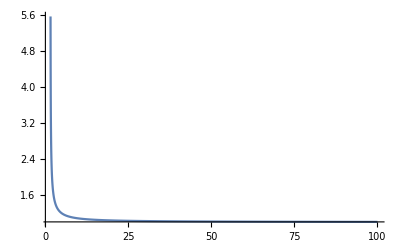

```mathematica
Plot[√(1/(1-3/(2 kappa))),{kappa,1.55,100},PlotRange->All]
```

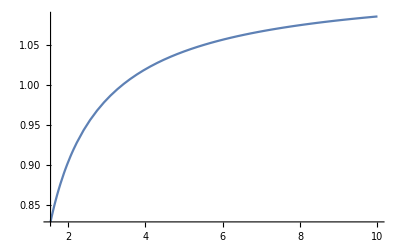

```mathematica
Plot[normK[941,110,kappa],{kappa,1.55,10},PlotRange->All]
```

```mathematica
normKFull[V_,kappa_]:=1/(π^(3/2)(2-3/kappa)^(3/2))(kappa^(3/2)/2 Gamma[kappa-1/2]/Gamma[kappa+1]+V/((2-3/kappa)^(1/2)π^(1/2))Hypergeometric2F1[1/2,kappa,3/2,-V^2/(2kappa -3)])^-1
barbKappaFull[vpar_,vperp_,V_,kappa_,alpha_]:=(1+(vpar^2+vperp^2+V^2-2 V(vpar^2+vperp^2(1-alpha))^(1/2))/(2 kappa - 3))^(-(kappa+1))UnitStep[vpar]
```

## α = 1 (no mirroring, so vanilla Maxwellian)

```mathematica
dPhi=941;
Tm=110;
```

Just so you know, the asymptotic value is

```mathematica
barbAsymp[dPhi,Tm]
```

18.1094

```mathematica
α=1;
```

```mathematica
Table[normK[dPhi,Tm,kaps]NIntegrate[vperp barbKappa[vpar,vperp,dPhi,Tm,kaps,α],{vpar,0,∞},{vperp,0,∞},AccuracyGoal->10,PrecisionGoal->10],{kaps,{100,50,25,15,10,5,3,2.5,2,1.6,1.55,1.52}}]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
NIntegrate[vperp barbDist[vpar,vperp,dPhi,Tm,α],{vpar,0,∞},{vperp,0,∞},AccuracyGoal->10,PrecisionGoal->10]
```

1.

Try full barbKappa

```mathematica
Table[NIntegrate[2 π vperp barbKappaFull[vpar,vperp,√(dPhi/Tm),kaps,α],{vpar,0,∞},{vperp,0,∞}],{kaps,{100,50,25,15,10,5,3,2.5,2,1.6,1.55,1.52}}]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

### Results for alpha= 0.5

```mathematica
α=0.5;
```

```mathematica
Table[normK[dPhi,Tm,kaps]NIntegrate[vperp barbKappa[vpar,vperp,dPhi,Tm,kaps,α],{vpar,0,∞},{vperp,0,∞},AccuracyGoal->10,PrecisionGoal->10],{kaps,{100,50,25,15,10,5,3,2.5,2,1.6,1.55,1.52}}]
```

{2.18963,2.18853,2.18618,2.18272,2.17793,2.16078,2.13239,2.11585,2.08712,2.03576,2.02242,2.01139}

```mathematica
NIntegrate[vperp barbDist[vpar,vperp,dPhi,Tm,α],{vpar,0,∞},{vperp,0,∞},AccuracyGoal->10,PrecisionGoal->10]
```

2.19067

```mathematica
Table[NIntegrate[2 π vperp barbKappaFull[vpar,vperp,√(dPhi/Tm),kaps,α],{vpar,0,∞},{vperp,0,∞},AccuracyGoal->10],{kaps,{100,50,25,15,10,5,3,2.5,2,1.6,1.55,1.52}}]
```

{2.2844,2.28147,2.27562,2.26784,2.25813,2.22886,2.18843,2.16668,2.1295,2.05826,2.03765,2.01972}

### Results for alpha= 0.2

```mathematica
α=0.2;
```

```mathematica
Table[normK[dPhi,Tm,kaps]NIntegrate[vperp barbKappa[vpar,vperp,dPhi,Tm,kaps,α],{vpar,0,∞},{vperp,0,∞},AccuracyGoal->10,PrecisionGoal->10],{kaps,{100,50,25,15,10,5,3,2.5,2,1.6,1.55,1.52}}]
```

{6.02717,6.01754,5.99824,5.97246,5.94015,5.84243,5.70761,5.63515,5.50963,5.24835,5.16477,5.08855}

```mathematica
NIntegrate[vperp barbDist[vpar,vperp,dPhi,Tm,α],{vpar,0,∞},{vperp,0,∞},AccuracyGoal->10,PrecisionGoal->10]
```

6.0368

```mathematica
Table[NIntegrate[2 π vperp barbKappaFull[vpar,vperp,√(dPhi/Tm),kaps,α],{vpar,0,∞},{vperp,0,∞},AccuracyGoal->10],{kaps,{100,50,25,15,10,5,3,2.5,2,1.6,1.55,1.52}}]
```

{5.01866,5.02577,5.04024,5.06007,5.08575,5.16846,5.28911,5.34973,5.42384,5.34259,5.25004,5.1448}

```mathematica
Table[NIntegrate[2 π vperp barbKappaFull[vpar,vperp,√(dPhi/Tm),kaps,α],{vpar,0,∞},{vperp,0,∞},AccuracyGoal->10],{kaps,{1000}}]
```

{5.01234}

### Results for alpha= 0.0001

```mathematica
α=0.0001;
```

```mathematica
Table[normK[dPhi,Tm,kaps]NIntegrate[vperp barbKappa[vpar,vperp,dPhi,Tm,kaps,α],{vpar,0,∞},{vperp,0,∞},AccuracyGoal->10,PrecisionGoal->10],{kaps,{100,50,25,15,10,5,3,2.5,2,1.6,1.55,1.52}}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{18.2714,18.4503,18.8253,19.3643,20.1098,22.9884,29.5195,35.2306,52.3215,187.285,352.415,826.12}

```mathematica
NIntegrate[vperp barbDist[vpar,vperp,dPhi,Tm,α],{vpar,0,∞},{vperp,0,∞},AccuracyGoal->10,PrecisionGoal->10]
```

18.0979

### Results for alpha= 10*^-9

```mathematica
α=10*^-9;
```

```mathematica
Table[normK[dPhi,Tm,kaps]NIntegrate[vperp barbKappa[vpar,vperp,dPhi,Tm,kaps,α],{vpar,0,∞},{vperp,0,∞},AccuracyGoal->10,PrecisionGoal->10],{kaps,{100,50,25,15,10,5,3,2.5,2,1.6,1.55,1.52}}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{18.2832,18.4624,18.8381,19.3782,20.1252,23.0103,29.5603,35.2926,52.4731,189.538,360.688,874.007}

```mathematica
NIntegrate[vperp barbDist[vpar,vperp,dPhi,Tm,α],{vpar,0,∞},{vperp,0,∞},AccuracyGoal->10,PrecisionGoal->10]
```

18.1094

### Results for alpha= 0

```mathematica
α=0;
```

```mathematica
Table[normK[dPhi,Tm,kaps]NIntegrate[vperp barbKappa[vpar,vperp,dPhi,Tm,kaps,α],{vpar,0,∞},{vperp,0,∞},AccuracyGoal->10,PrecisionGoal->10],{kaps,{100,50,25,15,10,5,3,2.5,2,1.6,1.55,1.52}}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{18.2832,18.4624,18.8381,19.3782,20.1252,23.0103,29.5603,35.2926,52.4731,189.538,360.688,874.012}

```mathematica
NIntegrate[vperp barbDist[vpar,vperp,dPhi,Tm,α],{vpar,0,∞},{vperp,0,∞},AccuracyGoal->10,PrecisionGoal->10]
```

18.1094